#### constants

```mathematica
c=137; (*speed of light*)
h = 6.63*10^(-34); (*Planck's constant*)
kb = 1.38*10^(-23)(*Boltzmann's constant   *);
e = 1;
me = 1;
ℏ = 1;
g = 9.81 (*acceleration of free fall*);
ϵ0=1/(4 Pi);
μ0= 4*Pi* 10 ^(-7) (*Permeability of free space*);
mp = 1.673*10^(-27) (*proton's rest mass*);
k = 1/(4*Pi*ϵ0) (*Columb's constant*);
Rh = 1.10 *10^7 (*Rydberg constant*);
a0 = 1;
α =1/137;
μb=e ℏ/(2 me); (* Bohr magneton *)
amu = 1.66054*10^(-27) (* atomic mass unit*);
E1 = 1/2;
```

#### functions

```mathematica
spinor[ms_] := Module[{sz},Sz::ms="'ms' is not an appropriate value of ms for this system.";
Which[ms == 1, sz = {1,0}, ms==-1, sz = {0,1}, True, Message[Sz::ms, ms]]
]; (* create spinor *)
insideSqrt[n_, l_]=(2/(n a0) )^3 ((n - l - 1)!)/(2 n  ((n + l)!));
secondHalf[n_,l_, r_]=Exp[- r / (n a0)]* (2 r/(n a0))^l * LaguerreL[n - l -1, 2 l +1, 2 r /(n a0)];
radialFcn[n_, l_, r_] =Sqrt[ insideSqrt[n,l]]*secondHalf[n,l,r];
```

#### Hydrogen wavefunction in | n, l, ml, ms > basis

```mathematica
Hydrogen[n_, l_, ml_,ms_,r_,θ_,ϕ_] = radialFcn[n,l,r]*SphericalHarmonicY[l, ml,θ, ϕ]*spinor[ms];
```

```mathematica
Integrate[Hydrogen[1,0,0,1,r,θ,ϕ]^2 r^2 Sin[θ], {r, 0, Infinity}, {θ, 0, Pi},{ϕ, 0, 2 Pi}]
```

∫_0^∞ ∫_0^π ∫_0^(2 π) r^2 Hydrogen[1,0,0,1,r,θ,ϕ]^2 Sin[θ]ⅆϕⅆθⅆr

#### Defining operators

```mathematica
asmps ={a0>0, ℏ>0, r>0, ϕ>0, θ>0};
Lz := ℏ / I (D[#, ϕ])&
Lp := ℏ Exp[ I ϕ](D[#, θ] + I Cot[θ]D[#,ϕ])&
Lm := ℏ Exp[ -I ϕ](-D[#, θ] + I Cot[θ]D[#,ϕ])&
Lx := 1/2 (Lp[#] + Lm[#])&
Ly := 1/2 *(-I) (Lp[#] - Lm[#])&
Sz = {{1,0},{0, -1}}*ℏ/2;
Sx = {{0,1},{1,0}}*ℏ/2;
Sy = {{0, -I},{I, 0}}*ℏ/2;
```

#### n=2 states

```mathematica
states[n_] := Flatten[Table[{n, i, j, k}, {i, 0, n-1}, {j, -i, i}, {k, -1, 1, 2}],2];
(* states in |n, l, ml, ms> *)
n2=states[2]
```

{{2,0,0,-1},{2,0,0,1},{2,1,-1,-1},{2,1,-1,1},{2,1,0,-1},{2,1,0,1},{2,1,1,-1},{2,1,1,1}}

#### W matrix part 1 fine structure

```mathematica
spinOrbit[stateNums_] := Module[{stateSet,matrix, i, j, row, elm, l, n},
stateSet = Table[Hydrogen@@Flatten[Append[stateNums[[i]], {r, θ, ϕ}]], {i, 1, Length[stateNums]}];
matrix = {};
For[i=1, i≤ Length[stateSet], i++,
row = {};
For[j=1, j≤ Length[stateSet], j++, 
elm = Integrate[Conjugate[stateSet[[i]]] .(Sz. Lz [stateSet[[j]]]+Sx. Lx [stateSet[[j]]]+Sy. Ly [stateSet[[j]]])/r^3*r^2 Sin[θ], {r, 0, Infinity}, {θ, 0, Pi}, {ϕ, 0, 2Pi}, Assumptions->asmps];
AppendTo[row, elm]
];
AppendTo[matrix, row]
];
matrix*(e^2/(8 Pi ϵ0 me^2 c^2))
];
```

```mathematica
relativistic[stateNums_] := Module[{matrix, i, j, row, elm, En, n, l},
matrix = {};
For[i=1, i≤ Length[stateNums], i++,
row = {};
For[j=1, j≤ Length[stateNums], j++, 
n=stateNums[[i,1]];
l=stateNums[[i,2]];
En = -E1/n^2;
If[j==i,elm = - (En)^2/(2 me c^2)(-3 +(4 n /(l + 1/2))),
elm= 0];
AppendTo[row, elm];
];
AppendTo[matrix, row]];
matrix];
```

```mathematica
darwinTerm[stateNums_]:= Module[{matrix, i, j, row, elm, En, n, l},
matrix = {};
For[i=1, i≤ Length[stateNums], i++,
row = {};
For[j=1, j≤ Length[stateNums], j++, 
n=stateNums[[i,1]];
l=stateNums[[i,2]];
En = -E1/n^2;
If[j==i&&l==0,elm = (En)^2/(me c^2)(2n),
elm= 0];
AppendTo[row, elm];
];
AppendTo[matrix, row]];
matrix];
```

```mathematica
fineStructure[stateNums_] := relativistic[stateNums] + spinOrbit[stateNums];
```

#### Zeeman effect

```mathematica
zeemanMatrix[stateNums_]:= Module[{matrix, i, j, row, elm, ml, ms},
matrix = {};
For[i=1, i≤ Length[stateNums], i++,
row = {};
For[j=1, j≤ Length[stateNums], j++, 
ml=stateNums[[i,3]];
ms=stateNums[[i,4]];
If[j==i,elm = μb Bext (ml + ms),
elm= 0];
AppendTo[row, elm];
];
AppendTo[matrix, row]];
matrix];
```

#### W matrix

```mathematica
wMatrix[stateNums_] := fineStructure[stateNums]+zeemanMatrix[stateNums];
```

#### Plot

```mathematica
plotZeeman[stateNums_, Bmin_, Bmax_]:= Module[{eigenvalues, w,plt},
w =wMatrix[stateNums]*27.2 -3.4;
eigenvalues = Eigenvalues[w];

plt =Plot[Chop[eigenvalues, 10^(-50)];, {Bext, Bmin, Bmax}, PlotRange->{-3.4 -3α^2, -3.4 +2α^2}, PlotLabel->"n=2 Zeeman splitting weak-Intermediate field", ImageSize->Large, AxesLabel->{"B_ext(T)", "E(eV)"}];
Show[plt]

];
```

```mathematica
m1=wMatrix[n2];
```

```mathematica
eigenvals1=Eigenvalues[m1]*27.2 -3.4;;
```

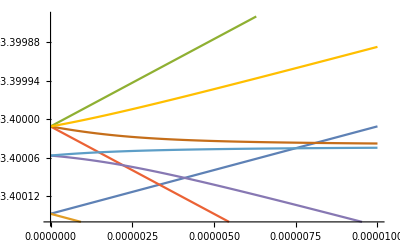

```mathematica
Plot[eigenvals1,{Bext, 0, .00001}, PlotRange->{-3.4-3(1/137)^2,-3.4 + 3α^2}]
```

```mathematica
w = wMatrix[n2]+darwinTerm[n2];
```

```mathematica
eigenvals = Eigenvalues[w]*27.2 -3.4;
```

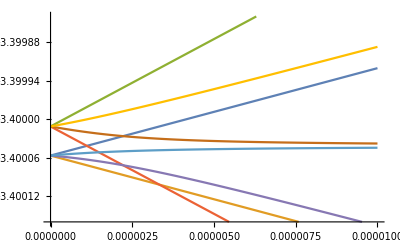

```mathematica
Plot[eigenvals,{Bext, 0, .00001}, PlotRange->{-3.4-3α^2,-3.4 + 3α^2}]
```